Here is the full model we are analyzing.

```mathematica
dTh1=b1+(c1 P)/(C1+P)+(s1 Th1^2)/(S1^2+Th1^2) I12/(I12+Th2) -m Th1;
dTh2=b2+(c2 P)/(C2+P)+(s2 Th2^2)/(S2^2+Th2^2) I21/(I21+Th1)-m Th2;
dP=bp P(1-P/Kp)-a P Th2;
```

I want to create a nondimensionalized version of this model, along the lines of the nondimensionalized version of the model I created earlier, so it will have the same nondimensional variables and parameters for the immunological dynamics (th_i = Th_i/S_i, τ = t m, β_i=b_i/(m S_i), σ_i=s_i/(m S_i), and ι_ij=i_ij/I_ij) plus the dimensionless parasite variable and parameters, p=P/K_p, κ_i=C_i/K_p, χ_i=c_i/(m S_i), ρ = b_p/m and α = a S_2/m.

```mathematica
dth1=Expand[that/TH1hat(dTh1/.{Th1->TH1hat th1,Th2->TH2hat th2,P->Phat p})/.{TH1hat->S1,TH2hat->S2,Phat->Kp,that->1/m}/.b1->β1 m S1/.s1->σ1 m S1/.I12->ι12 S2/.C1->κ1 Kp/.c1->χ1 m S1]//Simplify
dth2=Expand[that/TH2hat(dTh2/.{Th1->TH1hat th1,Th2->TH2hat th2,P->Phat p})/.{TH1hat->S1,TH2hat->S2,Phat->Kp,that->1/m}/.b2->β2 m S2/.s2->σ2 m S2/.I21->ι21 S1/.C2->κ2 Kp/.c2->χ2 m S2]//Simplify
dp=that/Phat(dP/.{Th1->TH1hat th1,Th2->TH2hat th2,P->Phat p})/.{TH1hat->S1,TH2hat->S2,Phat->Kp,that->1/m}/.bp->ρ m/.a->α m/S2//Expand
```

-th1+β1+(th1^2 ι12 σ1)/((1+th1^2) (th2+ι12))+(p χ1)/(p+κ1)

-th2+β2+(th2^2 ι21 σ2)/((1+th2^2) (th1+ι21))+(p χ2)/(p+κ2)

-p th2 α+p ρ-p^2 ρ

```mathematica
params={β1->b1/(m S1),β2->b2/(m S2),σ1->s1/(m S1),σ2->s2/(m S2),ι12->I12/S2,ι21->I21/S1,κ1->C1/Kp,κ2->C2/Kp,χ1->c1/(m S1),χ2->c2/(m S2),ρ->bp/m,α->(a S2)/m}/.{S1->1000,S2->1000,s1->2000,s2->2000,b1->0.1,b2->0.1,I12->10000,I21->10000,m->0.9,c1->100,c2->100,C1->50,C2->50,bp->3,Kp->300,a->0.003}
```

{β1→0.000111111,β2→0.000111111,σ1→2.22222,σ2→2.22222,ι12→10,ι21→10,κ1→1/6,κ2→1/6,χ1→0.111111,χ2→0.111111,ρ→3.33333,α→3.33333}

For this set of parameter values, there are four stable equilibria, representing an immune state with low activation and a chronic parasite, an immune state incorrectly polarized towards Th1 with a chronic parasite, a high co-activation equilibrium that almost clears the parasite, and an immune system correctly polarized towards Th2 with an acute infection.

```mathematica
pars=params;equils=Solve[{dth1==0,dth2==0,dp==0}/.pars,{th1,th2,p}];
(* Remove all negative equilibria *)
equils2=Delete[equils,Position[Table[If[NonNegative[equils[[i,1,2]]]&&NonNegative[equils[[i,2,2]]]&&NonNegative[equils[[i,3,2]]],True,False],{i,1,Length[equils]}],False]];
(* Remove all unstable equilibria *)
equils3=Delete[equils2,Position[Table[AllTrue[Negative[Re[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]]][[;;]]],TrueQ],{i,1,Length[equils2]}],False]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{th1→1.74767,th2→0.120665,p→0.879335},{th1→0.129609,th2→0.129609,p→0.870391},{th1→1.21747,th2→0.984702,p→0.0152976},{th1→0.000111135,th2→1.59565,p→0.}}

If you make the parasite provoke the immune response much more strongly (10x more strongly, e.g.), then the only stable equilibria represent acute infections (or an almost acute infection, anyway).

```mathematica
pars={β1->0.00011111111111111112,β2->0.00011111111111111112,σ1->2.2222222222222223,σ2->2.2222222222222223,ι12->10,ι21->10,κ1->1/6,κ2->1/6,χ1->1.11111111111111112,χ2->1.11111111111111112,ρ->3.3333333333333335,α->3.3333333333333335};
equils=Solve[{dth1==0,dth2==0,dp==0}/.pars,{th1,th2,p}];
(* Remove all negative equilibria *)
equils2=Delete[equils,Position[Table[If[NonNegative[equils[[i,1,2]]]&&NonNegative[equils[[i,2,2]]]&&NonNegative[equils[[i,3,2]]],True,False],{i,1,Length[equils]}],False]];
(* Remove all unstable equilibria *)
equils3=Delete[equils2,Position[Table[AllTrue[Negative[Re[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]]][[;;]]],TrueQ],{i,1,Length[equils2]}],False]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{th1→1.20315,th2→0.998777,p→0.00122318},{th1→0.000111135,th2→1.59565,p→0.}}

If you make cross-inhibition much stronger (100x stronger, e.g.), then the only stable equilibria are a low-activation equilibrium with a chronic parasite and a high Th2 equilibrium with an acute parasite.

```mathematica
pars={β1->0.00011111111111111112,β2->0.00011111111111111112,σ1->2.2222222222222223,σ2->2.2222222222222223,ι12->0.1,ι21->0.1,κ1->1/6,κ2->1/6,χ1->0.11111111111111112,χ2->0.11111111111111112,ρ->3.3333333333333335,α->3.3333333333333335};
equils=Solve[{dth1==0,dth2==0,dp==0}/.pars,{th1,th2,p}];
(* Remove all negative equilibria *)
equils2=Delete[equils,Position[Table[If[NonNegative[equils[[i,1,2]]]&&NonNegative[equils[[i,2,2]]]&&NonNegative[equils[[i,3,2]]],True,False],{i,1,Length[equils]}],False]];
(* Remove all unstable equilibria *)
equils3=Delete[equils2,Position[Table[AllTrue[Negative[Re[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]]][[;;]]],TrueQ],{i,1,Length[equils2]}],False]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{th1→0.105705,th2→0.105705,p→0.894295},{th1→0.000111113,th2→1.59162,p→0.}}

Across a wide range of parameter space, because cross-inhibition is soooo strong compared to self-activation, the parasite is able to reach a chronic infection because the immune system just wants to shut down.

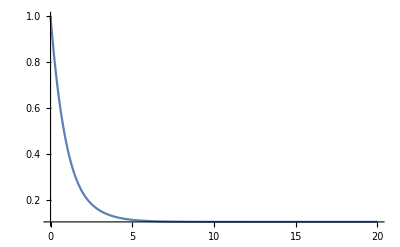

-Graphics-

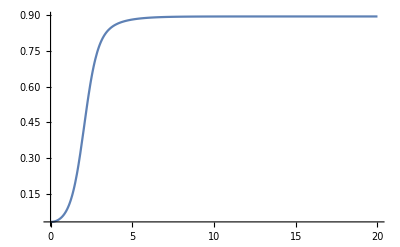

```mathematica
soln=NDSolve[{th1'[t]==(dth1/.{th1->th1[t],th2->th2[t],p->p[t]}),
th2'[t]==(dth2/.{th1->th1[t],th2->th2[t],p->p[t]}),
p'[t]==(dp/.{th1->th1[t],th2->th2[t],p->p[t]}),
th1[0]==1,th2[0]==1,p[0]==1/30}/.pars,{th1,th2,p},{t,0,100}];
Plot[th1[t]/.soln,{t,0,20},PlotRange->All]
Plot[th2[t]/.soln,{t,0,20},PlotRange->All]
Plot[p[t]/.soln,{t,0,20},PlotRange->All]
```

The only way to not have it shut down is for the immune system to start so strongly Th2 biased that it can’t help but go to that equilibrium.

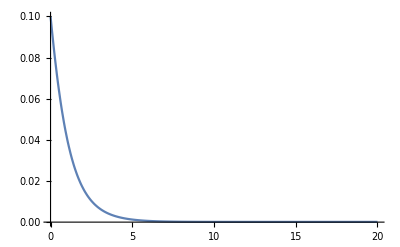

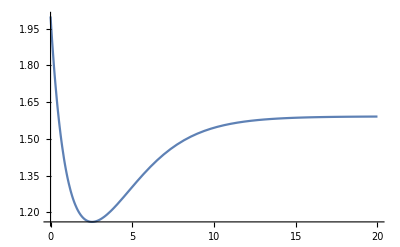

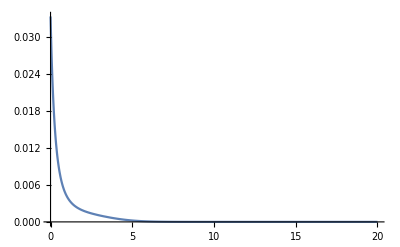

```mathematica
soln=NDSolve[{th1'[t]==(dth1/.{th1->th1[t],th2->th2[t],p->p[t]}),
th2'[t]==(dth2/.{th1->th1[t],th2->th2[t],p->p[t]}),
p'[t]==(dp/.{th1->th1[t],th2->th2[t],p->p[t]}),
th1[0]==0.1,th2[0]==2,p[0]==1/30}/.pars,{th1,th2,p},{t,0,100}];
Plot[th1[t]/.soln,{t,0,20},PlotRange->All]
Plot[th2[t]/.soln,{t,0,20},PlotRange->All]
Plot[p[t]/.soln,{t,0,20},PlotRange->All]
```

With weaker cross-inhibition, you see the emergence of a coexistence equilibrium that drives the parasite extinct, as well as the low-activation and Th1-biased equilibria where the parasite is chronic and the Th2-biased equilibrium where the parasite goes extinct.

```mathematica
pars={β1->0.00011111111111111112,β2->0.00011111111111111112,σ1->2.2222222222222223,σ2->2.2222222222222223,ι12->100,ι21->100,κ1->1/6,κ2->1/6,χ1->0.11111111111111112,χ2->0.11111111111111112,ρ->3.3333333333333335,α->3.3333333333333335};
equils=Solve[{dth1==0,dth2==0,dp==0}/.pars,{th1,th2,p}];
(* Remove all negative equilibria *)
equils2=Delete[equils,Position[Table[If[NonNegative[equils[[i,1,2]]]&&NonNegative[equils[[i,2,2]]]&&NonNegative[equils[[i,3,2]]],True,False],{i,1,Length[equils]}],False]];
(* Remove all unstable equilibria *)
equils3=Delete[equils2,Position[Table[AllTrue[Negative[Re[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]]][[;;]]],TrueQ],{i,1,Length[equils2]}],False]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{th1→1.78055,th2→0.129242,p→0.870758},{th1→0.130528,th2→0.130528,p→0.869472},{th1→1.53888,th2→1.53888,p→0.},{th1→0.000111138,th2→1.59568,p→0.}}

```mathematica
equils=Solve[{dth1==0,dth2==0,dp==0}/.params,{th1,th2,p}];
(* Remove all negative equilibria *)
equils2=Delete[equils,Position[Table[If[NonNegative[equils[[i,1,2]]]&&NonNegative[equils[[i,2,2]]]&&NonNegative[equils[[i,3,2]]],True,False],{i,1,Length[equils]}],False]];
(* Remove all unstable equilibria *)
equils3=Delete[equils2,Position[Table[AllTrue[Negative[Re[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.params/.equils2[[i]]]][[;;]]],TrueQ],{i,1,Length[equils2]}],False]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{th1→1.74767,th2→0.120665,p→0.879335},{th1→0.129609,th2→0.129609,p→0.870391},{th1→1.21747,th2→0.984702,p→0.0152976},{th1→0.000111135,th2→1.59565,p→0.}}

```mathematica
Re[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.params/.{th1->1.217466991194035,th2->0.9847024373547336,p->0.015297562645266372}]]
```

{-0.175182,-0.0353348,-0.0353348}

```mathematica
Table[{i0-1,(p[500]/.(NDSolve[{th1'[t]==(dth1/.{th1->th1[t],th2->th2[t],p->p[t]}),
th2'[t]==(dth2/.{th1->th1[t],th2->th2[t],p->p[t]}),
p'[t]==(dp/.{th1->th1[t],th2->th2[t],p->p[t]}),
th1[0]==i0,th2[0]==2-i0,p[0]==1/30}/.params,{th1,th2,p},{t,0,500}]))[[1]]},{i0,1,1.3,0.01}]
```

{{0.,-2.06516×10^-25},{0.01,0.879335},{0.02,0.879335},{0.03,0.0152976},{0.04,0.0152976},{0.05,0.0152976},{0.06,0.0152976},{0.07,0.0152976},{0.08,0.0152976},{0.09,0.0152976},{0.1,0.0152976},{0.11,0.0152976},{0.12,0.0152976},{0.13,0.0152976},{0.14,0.0152976},{0.15,0.0152976},{0.16,0.0152976},{0.17,0.0152976},{0.18,0.0152976},{0.19,0.0152976},{0.2,0.0152976},{0.21,0.0152976},{0.22,0.0152976},{0.23,0.0152976},{0.24,0.0152976},{0.25,0.0152976},{0.26,0.0152976},{0.27,0.0152976},{0.28,0.0152976},{0.29,0.879335},{0.3,0.879335}}

```mathematica
results=Table[Table[{p0,i0-1,(p[100]/.(NDSolve[{th1'[t]==(dth1/.{th1->th1[t],th2->th2[t],p->p[t]}),
th2'[t]==(dth2/.{th1->th1[t],th2->th2[t],p->p[t]}),
p'[t]==(dp/.{th1->th1[t],th2->th2[t],p->p[t]}),
th1[0]==i0,th2[0]==2-i0,p[0]==p0}/.params,{th1,th2,p},{t,0,100}]))[[1]]},{i0,0,2,0.01}],{p0,0.01,0.25,0.01}]
Export["~/immunoparasite/Dimensionless_results_across_immune_parasite_initials.csv" ,Flatten[results]]
```

```mathematica
params2={β1->0.00011111111111111112,β2->0.00011111111111111112,σ1->2.2222222222222223,σ2->2.2222222222222223,ι12->10,ι21->10,κ1->1/6,κ2->1/6,χ1->0.11111111111111112,χ2->1.5*0.11111111111111112,ρ->3.3333333333333335,α->3.3333333333333335};
results=Table[Table[{p0,i0-1,(p[100]/.(NDSolve[{th1'[t]==(dth1/.{th1->th1[t],th2->th2[t],p->p[t]}),
th2'[t]==(dth2/.{th1->th1[t],th2->th2[t],p->p[t]}),
p'[t]==(dp/.{th1->th1[t],th2->th2[t],p->p[t]}),
th1[0]==i0,th2[0]==2-i0,p[0]==p0}/.params2,{th1,th2,p},{t,0,100}]))[[1]]},{i0,0,2,0.01}],{p0,0.01,0.25,0.01}]
Export["~/immunoparasite/Dimensionless_results_across_immune_parasite_initials_stronger_induction_of_Th2.csv" ,Flatten[results]]
```

~/immunoparasite/Dimensionless_results_across_immune_parasite_initials_stronger_induction_of_Th2.csv

In the absence of any self-stimulation, the system behaves like a predator-prey system and the only stable equilibrium is one with a chronic infection.

```mathematica
pars={β1->0.00011111111111111112,β2->0.00011111111111111112,σ1->0,σ2->0,ι12->100,ι21->100,κ1->1/6,κ2->1/6,χ1->0.11111111111111112,χ2->1.5*0.11111111111111112,ρ->3.3333333333333335,α->3.3333333333333335};
equils=Solve[{dth1==0,dth2==0,dp==0}/.pars,{th1,th2,p}];
(* Remove all negative equilibria *)
equils2=Delete[equils,Position[Table[If[NonNegative[equils[[i,1,2]]]&&NonNegative[equils[[i,2,2]]]&&NonNegative[equils[[i,3,2]]],True,False],{i,1,Length[equils]}],False]];
(* Remove all unstable equilibria *)
equils3=Delete[equils2,Position[Table[AllTrue[Negative[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]][[;;]]],TrueQ],{i,1,Length[equils2]}],False]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{th1→0.0931895,th2→0.139729,p→0.860271}}

```mathematica
pars=params;equils=Solve[{dth1==0,dth2==0,dp==0}/.pars,{th1,th2,p}];
(* Remove all negative equilibria *)
equils2=Delete[equils,Position[Table[If[NonNegative[equils[[i,1,2]]]&&NonNegative[equils[[i,2,2]]]&&NonNegative[equils[[i,3,2]]],True,False],{i,1,Length[equils]}],False]];
(* Remove all unstable equilibria *)
equils3=Delete[equils2,Position[Table[AllTrue[Negative[Re[Eigenvalues[D[{dth1,dth2,dp},{{th1,th2,p}}]/.pars/.equils2[[i]]]][[;;]]],TrueQ],{i,1,Length[equils2]}],False]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{th1→1.74767,th2→0.120665,p→0.879335},{th1→0.129609,th2→0.129609,p→0.870391},{th1→1.21747,th2→0.984702,p→0.0152976},{th1→0.000111135,th2→1.59565,p→0.}}

```mathematica
results=Table[Table[Table[{toti,p0,2 i0/toti-1,(p[500]/.(NDSolve[{th1'[t]==(dth1/.{th1->th1[t],th2->th2[t],p->p[t]}),
th2'[t]==(dth2/.{th1->th1[t],th2->th2[t],p->p[t]}),
p'[t]==(dp/.{th1->th1[t],th2->th2[t],p->p[t]}),
th1[0]==i0,th2[0]==toti-i0,p[0]==p0}/.params,{th1,th2,p},{t,0,500}]))[[1]]},{i0,0,toti,toti/100}],{p0,0.01,0.25,0.0025}],{toti,0.1,2,0.1}]
Export["~/immunoparasite/Dimensionless_results_across_immune_parasite_initials_and_total_immune.csv" ,Flatten[results]]
```

~/immunoparasite/Dimensionless_results_across_immune_parasite_initials_and_total_immune.csv